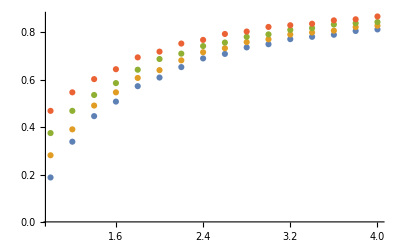

```mathematica
b={{1,6/(1×32)}, {1.2,13/(1.2×32)},{1.4,20/(1.4×32)},{1.6,26/(1.6×32)}, {1.8,33/(1.8×32)},{2,39/(2×32)},{2.2,46/(2.2×32)},{2.4,53/(2.4×32)},{2.6,59/(2.6×32)},{2.8,66/(2.8×32)},{3,72/(3×32)},{3.2,79/(3.2×32)},{3.4,85/(3.4×32)},{3.6,91/(3.6×32)},{3.8,98/(3.8×32)},{4,104/(4×32)}};
b2={{1,9/(1×32)}, {1.2,15/(1.2×32)},{1.4,22/(1.4×32)},{1.6,28/(1.6×32)}, {1.8,35/(1.8×32)},{2,41/(2×32)},{2.2,48/(2.2×32)},{2.4,55/(2.4×32)},{2.6,61/(2.6×32)},{2.8,68/(2.8×32)},{3,74/(3×32)},{3.2,81/(3.2×32)},{3.4,87/(3.4×32)},{3.6,93/(3.6×32)},{3.8,100/(3.8×32)},{4,106/(4×32)}};
b3={{1,12/(1×32)}, {1.2,18/(1.2×32)},{1.4,24/(1.4×32)},{1.6,30/(1.6×32)}, {1.8,37/(1.8×32)},{2,44/(2×32)},{2.2,50/(2.2×32)},{2.4,57/(2.4×32)},{2.6,63/(2.6×32)},{2.8,70/(2.8×32)},{3,76/(3×32)},{3.2,83/(3.2×32)},{3.4,89/(3.4×32)},{3.6,96/(3.6×32)},{3.8,102/(3.8×32)},{4,108/(4×32)}};
b4={{1,15/(1×32)}, {1.2,21/(1.2×32)},{1.4,27/(1.4×32)},{1.6,33/(1.6×32)}, {1.8,40/(1.8×32)},{2,46/(2×32)},{2.2,53/(2.2×32)},{2.4,59/(2.4×32)},{2.6,66/(2.6×32)},{2.8,72/(2.8×32)},{3,79/(3×32)},{3.2,85/(3.2×32)},{3.4,91/(3.4×32)},{3.6,98/(3.6×32)},{3.8,104/(3.8×32)},{4,111/(4×32)}};
ListPlot[{b,b2, b3,b4}]
```

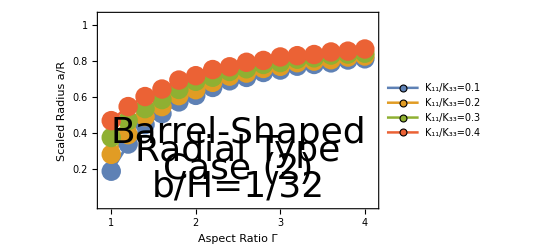

```mathematica
ListPlot[{b,b2,b3,b4},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1},None},{{1,1.5,2,2.5,3,3.5,4},None}}, PlotRange->{{0.9,4.1},{0,1.05}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=0.2","K_11/K_33=0.3","K_11/K_33=0.4"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Right, Bottom}],Epilog->{Text[Style["Barrel-Shaped",Directive[Black,36]],{2.5,0.4}],Text[Style["Radial Type",Directive[Black,36]],{2.5,0.3}],Text[Style["Case (2)",Directive[Black,36]],{2.5,0.2}],Text[Style["b/H=1/32",Directive[Black,36]],{2.5,0.1}]}]
```